```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210224_impacts_in_time_windows"];
```

```mathematica
datafull=Import["../data/ccm1_data_modified.csv",HeaderLines->2];
```

```mathematica
datafull[[1]]
```

{1,122,115686,CCM1,14.12.16,16000181-04,148956,#NAME?,1.24×10^6,87,2.74×10^9,3.35×10^9,16000181,26,0,0}

```mathematica
Dimensions@datafull
```

{459203,16}

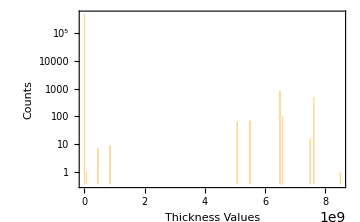
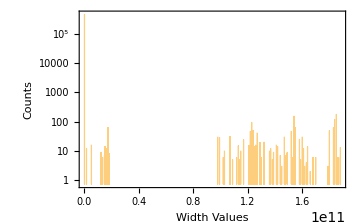

```mathematica
{Histogram[datafull[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
datafullnoNA=datafull/."NA"->0;
```

```mathematica
thickpos=Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#==2&)];
```

```mathematica
Length@thickpos
```

396299

```mathematica
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==12&)]]],11]]="NA";
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==12&)]]],12]]="NA";
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==12&)]]],10]]="NA";
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==12&)]]],9]]="NA";
```

```mathematica
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==7&)]]],11]]/=10^5;
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==7&)]]],12]]/=10^5;
datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#==7&)]]],9]]/=10^3;
```

```mathematica
density[thick_,width_,weight_,length_]:=N@weight/(thick*width*length)
```

```mathematica
(* KeySort@Counts@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[datafullnoNA[[Flatten@thickpos,9]]][[All,2]],_?(#≤4&)]]],9]] *)
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
```

```mathematica
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
KeySort@Counts@densities
```

<|-0.0003581→6,0→39,0.→7,7.37584×10^-14→8,7.40346×10^-14→8,7.42935×10^-14→6,7.44644×10^-14→7,7.45616×10^-14→12,7.46385×10^-14→4,7.46423×10^-14→7,7.47016×10^-14→14,7.47024×10^-14→7,7.47863×10^-14→6,7.48139×10^-14→6,17447,763.725→6,763.826→16,763.942→7,764.038→7,764.203→7,764.874→7,765.515→7,766.12→24,767.356→7,784.85→7,785.532→6,815.893→13,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
RealDigits@7.397848389825049*^-7
```

{{7,3,9,7,8,4,8,3,8,9,8,2,5,0,4,9},-6}

```mathematica
N@density[76,1640,38400,40300]
```

7.64485×10^-6

```mathematica
table1=datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-13&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table1[[Flatten@Position[RealDigits[table1[[All,5]]][[All,2]],_?(#==5&)],1]],11]]*=10^8;
datafullnoNA[[table1[[Complement[Range@Length@table1,Flatten@Position[RealDigits[table1[[All,5]]][[All,2]],_?(#==5&)]],1]],12]]/=10^4;
datafullnoNA[[table1[[Complement[Range@Length@table1,Flatten@Position[RealDigits[table1[[All,5]]][[All,2]],_?(#==5&)]],1]],11]]*=10^4;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,7.61481×10^-13→6,7.33946×10^-11→7,7.42199×10^-11→18,7.42908×10^-11→113,7.43068×10^-11→6,7.43192×10^-11→8,7.43213×10^-11→18,7.44576×10^-11→7,7.46484×10^-11→9,7.52724×10^-11→12,7.52992×10^-11→6,17379,763.725→6,763.826→16,763.942→7,764.038→7,764.203→7,764.874→7,765.515→7,766.12→24,767.356→7,784.85→7,785.532→6,815.893→13,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table2=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-10&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table2[[Flatten@Position[RealDigits[table2[[All,5]]][[All,2]],_?(#==5&)],1]],11]]*=10^5;
datafullnoNA[[table2[[Complement[Range@Length@table2,Flatten@Position[RealDigits[table2[[All,5]]][[All,2]],_?(#==5&)]],1]],12]]/=10^5;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,7.61481×10^-13→6,6.9973×10^-10→8,7.13662×10^-10→8,7.14097×10^-10→6,7.19109×10^-10→7,7.19364×10^-10→8,7.21697×10^-10→7,7.24491×10^-10→5,7.24668×10^-10→6,7.24685×10^-10→7,7.26247×10^-10→5,17367,763.725→6,763.826→16,763.942→7,764.038→7,764.203→7,764.874→7,765.515→7,766.12→24,767.356→7,784.85→7,785.532→6,815.893→13,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table3=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-9&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table3[[Flatten@Position[RealDigits[table3[[All,5]]][[All,2]],_?(#==5&)],1]],11]]*=10^4;
datafullnoNA[[table3[[Complement[Range@Length@table3,Flatten@Position[RealDigits[table3[[All,5]]][[All,2]],_?(#==5&)]],1]],12]]/=10^5;
datafullnoNA[[table3[[Complement[Range@Length@table3,Flatten@Position[RealDigits[table3[[All,5]]][[All,2]],_?(#==5&)]],1]],11]]/=10;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,7.61481×10^-13→6,7.34619×10^-9→7,7.35375×10^-9→7,7.46199×10^-9→14,7.47005×10^-9→6,7.48817×10^-9→8,7.50484×10^-9→14,7.51794×10^-9→14,7.52694×10^-9→5,7.54579×10^-9→6,7.55551×10^-9→7,16245,763.725→6,763.826→16,763.942→7,764.038→7,764.203→7,764.874→7,765.515→7,766.12→24,767.356→7,784.85→7,785.532→6,815.893→13,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table4=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-8&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table4[[Flatten@Position[RealDigits[table4[[All,5]]][[All,2]],_?(#==4&)],1]],11]]*=10^3;
datafullnoNA[[table4[[Complement[Range@Length@table4,Flatten@Position[RealDigits[table4[[All,5]]][[All,2]],_?(#==4&)]],1]],12]]/=10^5;
datafullnoNA[[table4[[Complement[Range@Length@table4,Flatten@Position[RealDigits[table4[[All,5]]][[All,2]],_?(#==4&)]],1]],11]]/=10^2;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,7.61481×10^-13→6,7.3302×10^-7→5,7.39785×10^-7→5,7.40713×10^-7→4,7.42905×10^-7→4,7.43071×10^-7→4,7.43187×10^-7→4,7.43362×10^-7→4,7.43452×10^-7→5,7.43898×10^-7→8,7.44067×10^-7→7,7.44465×10^-7→5,16219,763.725→6,763.826→16,763.942→7,764.038→7,764.203→7,764.874→7,765.515→7,766.12→24,767.356→7,784.85→7,785.532→6,815.893→13,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
RealDigits@3.91*^9
```

{{3,9,1,0,0,0,0,0,0,0,0,0,0,0,0,0},10}

```mathematica
table5=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-6&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==5&)],1]],11]]*=10;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==6&)],1]],12]]/=10;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==1&)],1]],11]]*=10^4;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==1&)],1]],12]]*=10^3;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==10&)],1]],11]]/=10^4;
datafullnoNA[[table5[[Flatten@Position[RealDigits[table5[[All,5]]][[All,2]],_?(#==10&)],1]],12]]/=10^5;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,7.61481×10^-13→6,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.88634×10^-6→8,6.91767×10^-6→7,6.92681×10^-6→7,6.93044×10^-6→7,6.94229×10^-6→8,6.95279×10^-6→8,6.98525×10^-6→7,16120,763.725→6,763.826→16,763.942→7,764.038→7,764.203→7,764.874→7,765.515→7,766.12→24,767.356→7,784.85→7,785.532→6,815.893→13,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table6=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-12&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table6[[Flatten@Position[RealDigits[table6[[All,5]]][[All,2]],_?(#==4&)],1]],11]]*=10^7;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.88634×10^-6→8,6.91767×10^-6→7,6.92681×10^-6→7,6.93044×10^-6→7,6.94229×10^-6→8,6.95279×10^-6→8,6.98525×10^-6→7,6.9917×10^-6→9,16119,763.725→6,763.826→16,763.942→7,764.038→7,764.203→7,764.874→7,765.515→7,766.12→24,767.356→7,784.85→7,785.532→6,815.893→13,817.867→7,827.775→6|>
 |  |  |  |

```mathematica
table7=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==3&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table7[[Flatten@Position[RealDigits[table7[[All,4]]][[All,2]],_?(#==5&)],1]],12]]*=10^8;
datafullnoNA[[table7[[Flatten@Position[RealDigits[table7[[All,4]]][[All,2]],_?(#==4&)],1]],12]]*=10^8;
datafullnoNA[[table7[[Flatten@Position[RealDigits[table7[[All,4]]][[All,2]],_?(#==10&)],1]],11]]/=10^5;
datafullnoNA[[table7[[Flatten@Position[RealDigits[table7[[All,4]]][[All,2]],_?(#==10&)],1]],12]]*=10^3;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.88634×10^-6→8,6.91767×10^-6→7,6.92681×10^-6→7,6.93044×10^-6→7,6.94229×10^-6→8,6.95279×10^-6→8,6.98525×10^-6→7,6.9917×10^-6→9,16039,0.76043→6,0.761083→7,0.761389→5,0.761861→16,0.762056→6,0.762454→7,0.762842→12,0.763504→5,0.76365→7,0.763834→12,0.764051→9,0.765272→7,0.766903→7,9.28829→24|>
 |  |  |  |

```mathematica
table8=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==0&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table8[[Flatten@Position[RealDigits[table8[[All,4]]][[All,2]],_?(#==5&)],1]],12]]*=10^5;
datafullnoNA[[table8[[Flatten@Position[RealDigits[table8[[All,4]]][[All,2]],_?(#==10&)],1]],11]]/=10^5;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.88634×10^-6→8,6.91767×10^-6→7,6.92681×10^-6→7,6.93044×10^-6→7,6.94229×10^-6→8,6.95279×10^-6→8,6.98525×10^-6→7,6.9917×10^-6→9,16018,0.0782279→4,0.0784704→8,0.0785401→4,0.0785505→8,0.0794567→7,0.079572→6,0.0799779→7,0.081693→8,0.0817012→6,0.0823354→7,0.0825568→7,0.0825856→7,0.0837549→7,9.28829→24|>
 |  |  |  |

```mathematica
RealDigits@0.07854014074393222
```

{{7,8,5,4,0,1,4,0,7,4,3,9,3,2,2,2},-1}

```mathematica
table9=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-1&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==5&)],1]],12]]*=10^4;datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==4&)],1]],12]]*=10^4;
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==1&)],1]],11]]*=10^4;
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==1&)],1]],12]]*=10^8;
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==10&)],1]],11]]/=10^5;
datafullnoNA[[table9[[Flatten@Position[RealDigits[table9[[All,4]]][[All,2]],_?(#==10&)],1]],12]]/=10^1;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,1.03544×10^-6→5,3.3906×10^-6→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.88634×10^-6→8,6.91767×10^-6→7,6.92681×10^-6→7,6.93044×10^-6→7,6.94229×10^-6→8,15027,0.0000781852→8,0.000078394→8,0.0000824377→5,0.000192284→7,0.00115906→7,0.00134858→7,0.00747228→5,0.00754268→4,0.00755948→4,0.00756265→5,0.00758101→6,0.076598→3,9.28829→24|>
 |  |  |  |

```mathematica
table10=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-2&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table10[[Flatten@Position[RealDigits[table10[[All,4]]][[All,2]],_?(#==4&)],1]],12]]*=10^3;
datafullnoNA[[table10[[Flatten@Position[RealDigits[table10[[All,4]]][[All,2]],_?(#==3&)],1]],11]]*=10^1;datafullnoNA[[table10[[Flatten@Position[RealDigits[table10[[All,4]]][[All,2]],_?(#==3&)],1]],12]]*=10^4;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,1.03544×10^-6→5,1.15906×10^-6→7,1.34858×10^-6→7,3.3906×10^-6→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.88634×10^-6→8,6.91767×10^-6→7,6.92681×10^-6→7,15024,0.0000766171→7,0.0000766196→8,0.0000766271→21,0.0000767256→7,0.0000767277→7,0.0000767737→6,0.0000780236→4,0.0000781852→8,0.000078394→8,0.0000824377→5,0.000192284→7,0.076598→3,9.28829→24|>
 |  |  |  |

```mathematica
table11=N@datafullnoNA[[Flatten@thickpos[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-4&)]]],{1,9,10,11,12,13}]];
```

```mathematica
datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==5&)],1]],12]]*=10^1;
datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==1&)],1]],11]]*=10^3;datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==1&)],1]],12]]*=10^4;datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==10&)],1]],11]]/=10^6;
datafullnoNA[[table11[[Flatten@Position[RealDigits[table11[[All,4]]][[All,2]],_?(#==10&)],1]],12]]/=10^5;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,1.03544×10^-6→5,1.15906×10^-6→7,1.34858×10^-6→7,3.3906×10^-6→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.87581×10^-6→6,6.88634×10^-6→8,6.91767×10^-6→7,14486,8.46265×10^-6→7,8.46572×10^-6→7,8.47446×10^-6→7,8.4763×10^-6→7,8.48076×10^-6→7,8.51343×10^-6→7,8.51626×10^-6→7,8.60324×10^-6→7,8.60358×10^-6→7,0.0000755073→7,0.000192284→7,0.076598→3,9.28829→24|>
 |  |  |  |

```mathematica
datafullnoNA[[Flatten@thickpos[[Flatten@Position[densities,0.00007550731477111845]]],11]]/=10^1;
datafullnoNA[[Flatten@thickpos[[Flatten@Position[densities,0.07659796061714341]]],11]]/=10^5;
datafullnoNA[[Flatten@thickpos[[Flatten@Position[densities,0.07659796061714341]]],12]]/=10^1;
```

```mathematica
thickvaluesthkpos=datafullnoNA[[Flatten@thickpos,10]];
widthvaluesthkpos=datafullnoNA[[Flatten@thickpos,9]];
weightvaluesthkpos=datafullnoNA[[Flatten@thickpos,11]];
lengthvaluesthkpos=datafullnoNA[[Flatten@thickpos,12]];
densities=Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],weightvaluesthkpos[[i]],lengthvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.Indeterminate->0;
KeySort@Counts@densities
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

<|-0.0003581→6,0→39,0.→7,1.03544×10^-6→5,1.15906×10^-6→7,1.34858×10^-6→7,3.3906×10^-6→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.87581×10^-6→6,6.88634×10^-6→8,6.91767×10^-6→7,14485,8.45417×10^-6→7,8.4573×10^-6→5,8.46265×10^-6→7,8.46572×10^-6→7,8.47446×10^-6→7,8.4763×10^-6→7,8.48076×10^-6→7,8.51343×10^-6→7,8.51626×10^-6→7,8.60324×10^-6→7,8.60358×10^-6→7,0.000192284→7,9.28829→24|>
 |  |  |  |

```mathematica
Length@densities
Length@densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]]
```

396299

396216

```mathematica
KeySort@Counts@densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]]
```

<|1.03544×10^-6→5,1.15906×10^-6→7,1.34858×10^-6→7,3.3906×10^-6→7,6.78278×10^-6→10,6.85114×10^-6→8,6.87191×10^-6→3,6.87581×10^-6→6,6.88634×10^-6→8,6.91767×10^-6→7,6.92681×10^-6→7,6.93044×10^-6→7,6.94229×10^-6→8,14481,8.43639×10^-6→7,8.45417×10^-6→7,8.4573×10^-6→5,8.46265×10^-6→7,8.46572×10^-6→7,8.47446×10^-6→7,8.4763×10^-6→7,8.48076×10^-6→7,8.51343×10^-6→7,8.51626×10^-6→7,8.60324×10^-6→7,8.60358×10^-6→7|>
 |  |  |  |

suitable densities belong to rows that will be considered in the dataset

```mathematica
Length@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]
```

396190

```mathematica
datafullnoNA[[Flatten@thickpos[[Complement[Range@Length@densities,Flatten@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]]]],11]]="NA";
datafullnoNA[[Flatten@thickpos[[Complement[Range@Length@densities,Flatten@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]]]],12]]="NA";
datafullnoNA[[Flatten@thickpos[[Complement[Range@Length@densities,Flatten@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]]]],10]]="NA";
datafullnoNA[[Flatten@thickpos[[Complement[Range@Length@densities,Flatten@Position[densities[[Flatten@Position[RealDigits[densities][[All,2]],_?(#==-5&)]]],_?(#>6*^-6&)]]]],9]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Complement[Range@Length@datafullnoNA,Flatten@Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#≤2&)]],11]]="NA";
datafullnoNA[[Complement[Range@Length@datafullnoNA,Flatten@Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#≤2&)]],12]]="NA";
datafullnoNA[[Complement[Range@Length@datafullnoNA,Flatten@Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#≤2&)]],9]]="NA";
datafullnoNA[[Complement[Range@Length@datafullnoNA,Flatten@Position[RealDigits[datafullnoNA[[All,10]]][[All,2]],_?(#≤2&)]],10]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[Flatten@Position[datafullnoNA[[All,9]],_?(#>10^9&)],12]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,9]],_?(#>10^9&)],11]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,9]],_?(#>10^9&)],10]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,9]],_?(#>10^9&)],9]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

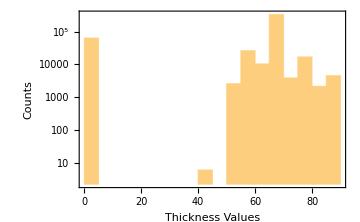
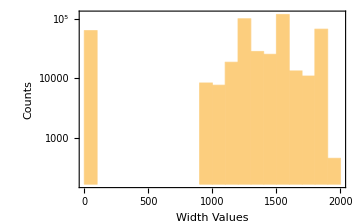
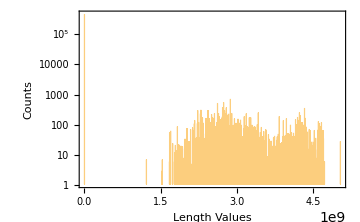
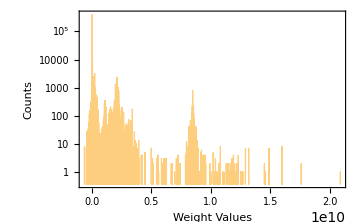

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium]}(*,Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->{{0,10^7},All},Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],ScalingFunctions->"Log",PlotRange->{{-100,10^7},All},Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium]}*)
```

```mathematica
Length@Position[datafullnoNA[[All,10]],0]
Length@Position[datafullnoNA[[All,11]],0]
```

61327

10491

```mathematica
weightpos=Complement[Range@Length@datafullnoNA,Flatten@Join[Position[datafullnoNA[[All,10]],0],Position[datafullnoNA[[All,10]],0.]]];
```

```mathematica
KeySort@Counts[N@datafullnoNA[[weightpos,11]]];
```

```mathematica
RealDigits@2.6*^7
```

{{2,6,0,0,0,0,0,0,0,0,0,0,0,0,0,0},8}

```mathematica
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==10&)]]],12]]/=10^6;
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==10&)]]],11]]/=10^6;
```

```mathematica
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==9&)]]],12]]/=10^5;
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==9&)]]],11]]/=10^5;
```

```mathematica
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==8&)]]],12]]/=10^4;
datafullnoNA[[Flatten@weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==8&)]]],11]]/=10^4;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],2.6*^7]]],9]]="NA";
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],2.6*^7]]],10]]="NA";
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],2.6*^7]]],12]]="NA";
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],2.6*^7]]],11]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==6&)]]],12]]/=10;
datafullnoNA[[weightpos[[Flatten@Position[RealDigits[datafullnoNA[[weightpos,11]]][[All,2]],_?(#==6&)]]],11]]/=10;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(#≥26700&)]]],12]]/=10;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(#≥26700&)]]],11]]/=10;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(400≤#<2670&)]]],12]]*=10;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(400≤#<2670&)]]],11]]*=10;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(3<#<4&)]]],12]]*=1000;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(3<#<4&)]]],11]]*=1000;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(1<#<3&)]]],12]]*=10000;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(1<#<3&)]]],11]]*=10000;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(0.01<#<1&)]]],12]]*=1000000;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(0.01<#<1&)]]],11]]*=1000000;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(10^(-4)<#<0.01&)]]],12]]*=10^8;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(10^(-4)<#<0.01&)]]],11]]*=10^8;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(10^(-5)<#<10^(-4)&)]]],12]]*=10^9;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?(10^(-5)<#<10^(-4)&)]]],11]]*=10^9;
```

```mathematica
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?Negative]]],12]]*=10^7;
datafullnoNA[[weightpos[[Flatten@Position[datafullnoNA[[weightpos,11]],_?Negative]]],11]]*=-10^7;
```

```mathematica
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],_?(#>80000&)],9]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],_?(#>80000&)],10]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],_?(#>80000&)],11]]="NA";
datafullnoNA[[Flatten@Position[datafullnoNA[[All,12]],_?(#>80000&)],12]]="NA";
datafullnoNA=datafullnoNA/."NA"->0.;
```

```mathematica
KeySort@Counts[N@datafullnoNA[[weightpos,11]]];
```

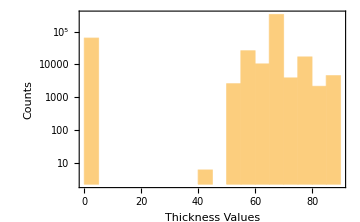
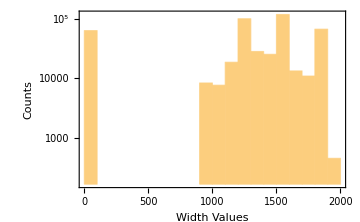
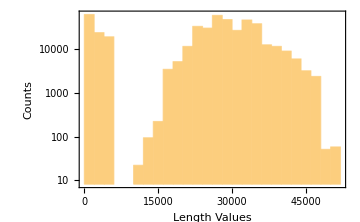
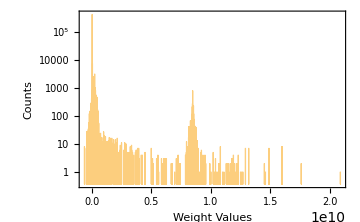

```mathematica
{Histogram[datafullnoNA[[All,10]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,12]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Length Values","Counts"},ImageSize->Medium],Histogram[datafullnoNA[[All,11]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Weight Values","Counts"},ImageSize->Medium]}
```

```mathematica
Length@Position[datafullnoNA[[All,10]],0]
Length@Position[datafullnoNA[[All,11]],0]
```

61327

10491

```mathematica
weightpos=Complement[Range@Length@datafullnoNA,Flatten@Join[Position[datafullnoNA[[All,10]],0],Position[datafullnoNA[[All,10]],0.]]];
```

```mathematica
N@9700/(1510*66*94000)
```

1.03544×10^-6